0.5

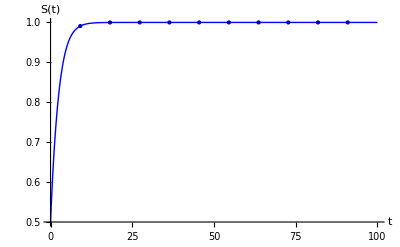

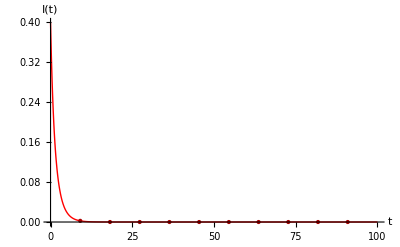

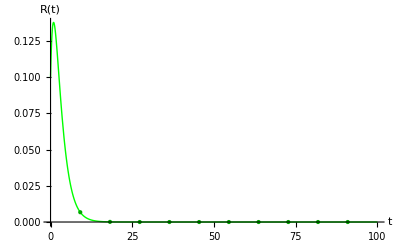

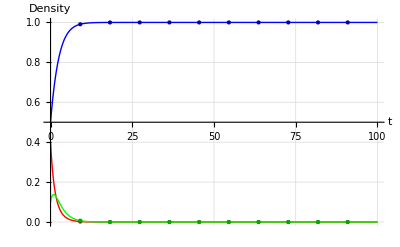

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=μ n-μ s[t]-β * s[t]*i[t]/n;
eq2=β*s[t]*i[t]/n-(μ+γ)*i[t];
eq3=γ*i[t]-μ r[t];
n=1;
μ=0.6;
β=0.5;
γ=0.4;
R0=N[β/(γ+μ)]
tf=100;
szero=0.5;
izero=0.4;
rzero=0.1;

sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3,s[0]==szero,i[0]==izero,r[0]==rzero},{s,i,r},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"R"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For R[t] versus t *)
plot3a=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"R(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol],Evaluate[r[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)","R(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

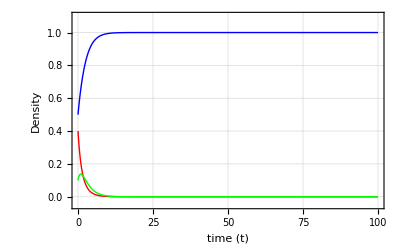

1.

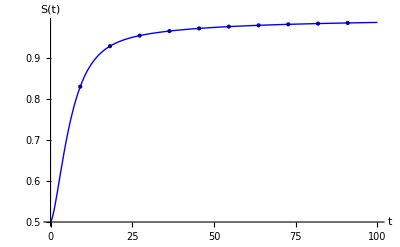

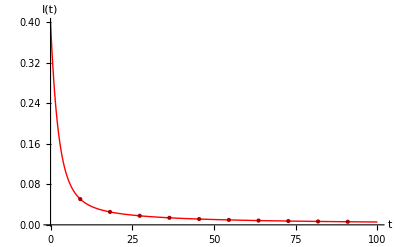

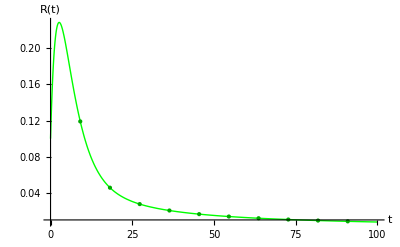

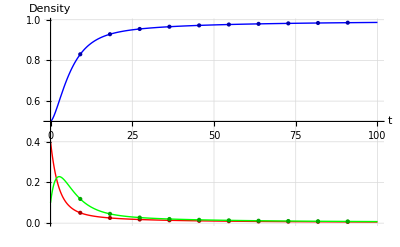

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=μ n-μ s[t]-β * s[t]*i[t]/n;
eq2=β*s[t]*i[t]/n-(μ+γ)*i[t];
eq3=γ*i[t]-μ r[t];
n=1;
μ=0.3;
β=0.7;
γ=0.4;
R0=N[β/(γ+μ)]
tf=100;
szero=0.5;
izero=0.4;
rzero=0.1;

sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3,s[0]==szero,i[0]==izero,r[0]==rzero},{s,i,r},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"R"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For R[t] versus t *)
plot3a=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"R(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol],Evaluate[r[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)","R(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]
```

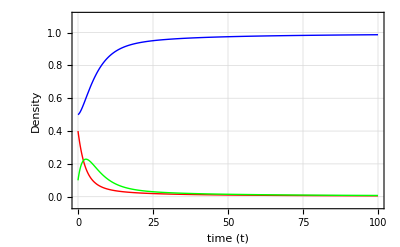

1.2

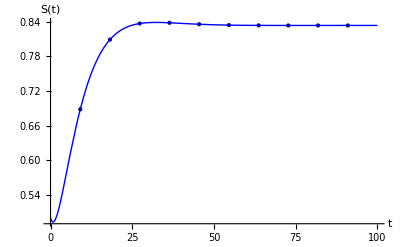

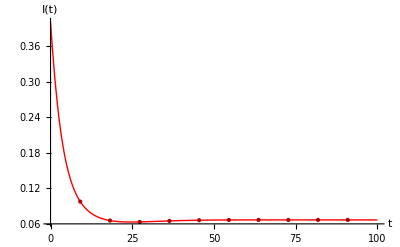

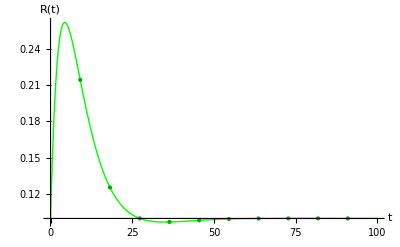

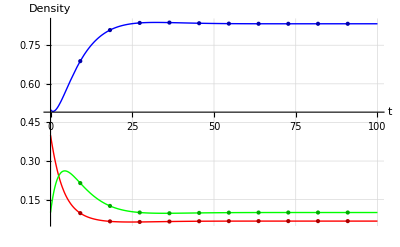

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=μ n-μ s[t]-β * s[t]*i[t]/n;
eq2=β*s[t]*i[t]/n-(μ+γ)*i[t];
eq3=γ*i[t]-μ r[t];
n=1;
μ=0.2;
β=0.6;
γ=0.3;
R0=N[β/(γ+μ)]
tf=100;
szero=0.5;
izero=0.4;
rzero=0.1;

sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3,s[0]==szero,i[0]==izero,r[0]==rzero},{s,i,r},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"R"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For R[t] versus t *)
plot3a=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"R(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol],Evaluate[r[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)","R(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]
```

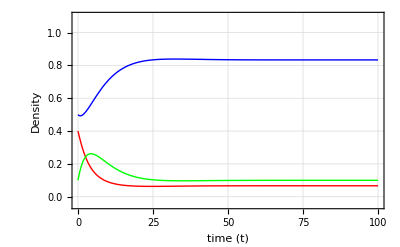

```mathematica
(*This is example of Tunnel Diode Example*)Clear["Global`*"]

eq1=μ n-μ s[t]-β * s[t]*i[t]/n;
eq2=β*s[t]*i[t]/n-(μ+γ)*i[t];
eq3=γ*i[t]-μ r[t];
n=1;
μ=0.3;
β=0.8;
γ=0.2;
R0=N[β/(γ+μ)]
St=n/R0
It=(n μ (R0-1))/β
tf=50;
num=10;

szero[0]=1.0;
izero[0]=0.0;
rzero[0]=0.0;

szero[1]=0.9;
izero[1]=0.1;
rzero[1]=0.0;

szero[2]=0.8;
izero[2]=0.2;
rzero[2]=0.0;

szero[3]=0.7;
izero[3]=0.3;
rzero[3]=0.0;

szero[4]=0.6;
izero[4]=0.4;
rzero[4]=0.0;

szero[5]=0.5;
izero[5]=0.5;
rzero[5]=0.0;

szero[6]=0.4;
izero[6]=0.6;
rzero[6]=0.0;

szero[7]=0.3;
izero[7]=0.7;
rzero[7]=0.0;

szero[8]=0.2;
izero[8]=0.8;
rzero[8]=0.0;

szero[9]=0.1;
izero[9]=0.9;
rzero[9]=0.0;

szero[10]=0.0;
izero[10]=1.0;
rzero[10]=0.0;


Do[sol[k]=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3, s[0]==szero[k],i[0]==izero[k],r[0]==rzero[k]},{s,i,r},{t,tf}],{k,0,num}]


pl[k_]:=ParametricPlot[Evaluate[{s[t],i[t]}/.sol[k]],{t,0,tf},PlotRange->All]

pls=Flatten[Table[pl[k],{k,0,num}]];
line = Graphics[Line[{{0,1.0},{1.0,0}}]];
arrow=Graphics[{Arrowheads[0.03],Arrow[{{0.5,0.6},{0.45,0.55}}]}];
Show[pls,line,arrow,PlotRange->{{0.1,0.9},{0.1,0.9}},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Infected (I)",""},{"Susceptible "[S],""}}]
```

1.6

0.625

0.225

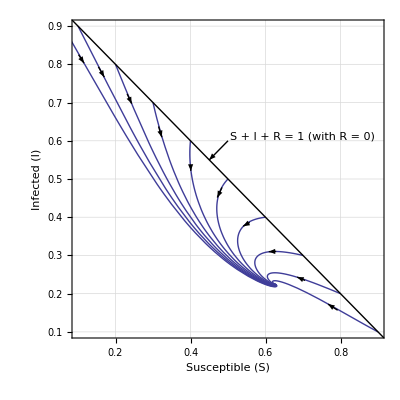

```mathematica
(*This is example of Tunnel Diode Example*)Clear["Global`*"]

eq1=μ n-μ s[t]-β * s[t]*i[t]/n;
eq2=β*s[t]*i[t]/n-(μ+γ)*i[t];
eq3=γ*i[t]-μ r[t];
n=1;
μ=0.6;
β=0.5;
γ=0.4;
R0=N[β/(γ+μ)]
St=n/R0
It=(n μ (R0-1))/β
tf=50;
num=10;

szero[0]=1.0;
izero[0]=0.0;
rzero[0]=0.0;

szero[1]=0.9;
izero[1]=0.1;
rzero[1]=0.0;

szero[2]=0.8;
izero[2]=0.2;
rzero[2]=0.0;

szero[3]=0.7;
izero[3]=0.3;
rzero[3]=0.0;

szero[4]=0.6;
izero[4]=0.4;
rzero[4]=0.0;

szero[5]=0.5;
izero[5]=0.5;
rzero[5]=0.0;

szero[6]=0.4;
izero[6]=0.6;
rzero[6]=0.0;

szero[7]=0.3;
izero[7]=0.7;
rzero[7]=0.0;

szero[8]=0.2;
izero[8]=0.8;
rzero[8]=0.0;

szero[9]=0.1;
izero[9]=0.9;
rzero[9]=0.0;

szero[10]=0.0;
izero[10]=1.0;
rzero[10]=0.0;


Do[sol[k]=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3, s[0]==szero[k],i[0]==izero[k],r[0]==rzero[k]},{s,i,r},{t,tf}],{k,0,num}]


pl[k_]:=ParametricPlot[Evaluate[{s[t],i[t]}/.sol[k]],{t,0,tf},PlotRange->All]

pls=Flatten[Table[pl[k],{k,0,num}]];
line = Graphics[Line[{{0,1.0},{1.0,0}}]];
arrow=Graphics[{Arrowheads[0.03],Arrow[{{0.5,0.6},{0.45,0.55}}]}];
Show[pls,line,arrow,PlotRange->{{0.0,1.01},{-0.01,1.0}},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Infected (I)",""},{"Susceptible "[S],""}}]
```

0.5

2.

-0.6

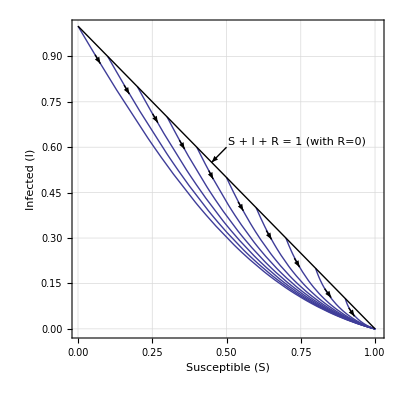

1.6

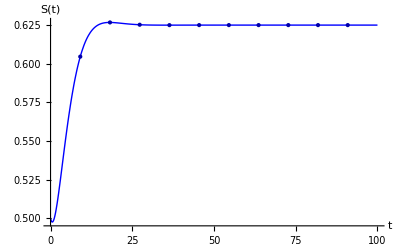

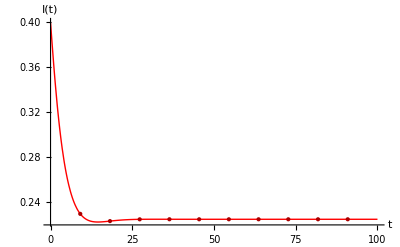

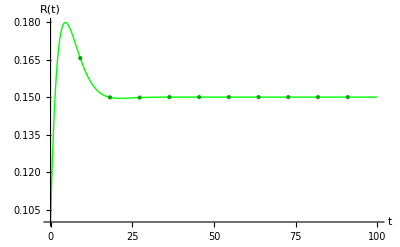

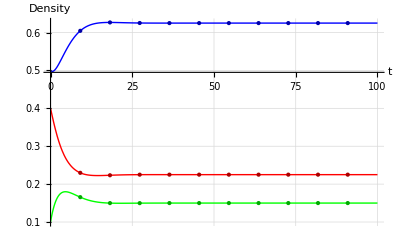

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=μ n-μ s[t]-β * s[t]*i[t]/n;
eq2=β*s[t]*i[t]/n-(μ+γ)*i[t];
eq3=γ*i[t]-μ r[t];
n=1;
μ=0.3;
β=0.8;
γ=0.2;
R0=N[β/(γ+μ)]
tf=100;
szero=0.5;
izero=0.4;
rzero=0.1;

sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3,s[0]==szero,i[0]==izero,r[0]==rzero},{s,i,r},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"R"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For R[t] versus t *)
plot3a=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"R(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol],Evaluate[r[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)","R(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]
```

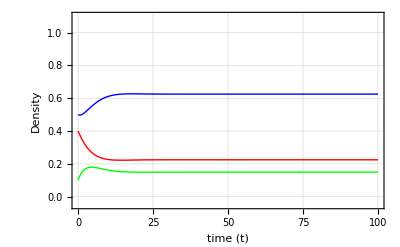

```mathematica
min=0;
max = 1.0;
n=1;
c=1.5;
arrow=Graphics[{Arrowheads[0.03],Arrow[{{0.9,0.2},{0.9999,0.01}}]}];
aa1=Plot[Piecewise[{{0,r0<1},{(r0-1)*n*c,r0>1}}],{r0,0,1.5},PlotRange->{{0.5,1.5},{-0.1,1.1}},PlotStyle->{Thick, Magenta},GridLines->{{},{min}},GridLinesStyle-> Directive[Dashed, Gray],Frame->{True,True,True,True},FrameLabel->{{"Infected Fraction, I(t)",""},{"Basic Reproduction Ratio (R_0)",""}}];

Show[{aa1,arrow}]
```

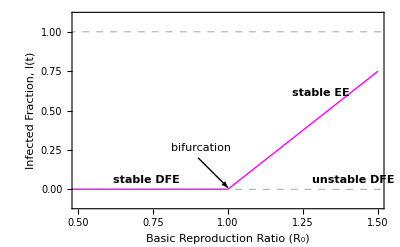

```mathematica
hgj
```